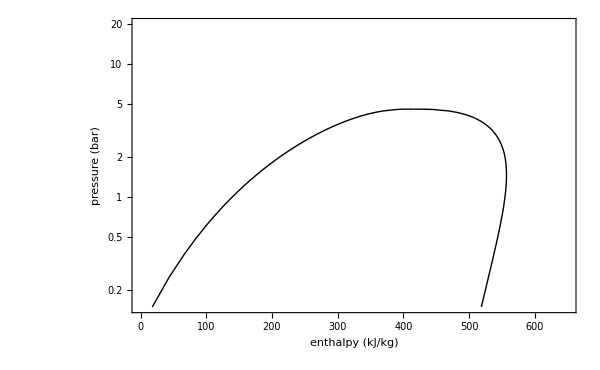

```mathematica
Module[{HL,HV},
HL={{11.509,0.132},{43.758,0.252},{66.357,0.372},{84.405,0.492},{99.738,0.612},{113.25,0.732},{125.44,0.852},{136.641,0.972},{147.05,1.092},{156.83,1.212},{166.09,1.332},{174.922,1.452},{183.391,1.572},{191.55,1.692},{199.452,1.812},{207.12,1.932},{214.59,2.052},{221.9,2.172},{229.08,2.29203},{236.13,2.412},{243.09,2.532},{249.982,2.652},{256.82,2.77202},{263.61,2.892},{270.4,3.012},{277.2,3.132},{284.02,3.25202},{290.91,3.372},{297.903,3.492},{305.01,3.612},{312.32,3.732},{319.87,3.852},{327.783,3.972},{336.19,4.09205},{345.35,4.212},{355.75,4.332},{368.6,4.452},{390.18,4.572},{391.72,4.57605},{394.79,4.58405},{399.13,4.59205},{415.593,4.599}};
HV={{516.2,0.132},{529.79,0.252},{537.91,0.372},{543.47,0.492},{547.52,0.612},{550.54,0.732},{552.81,0.852},{554.49,0.972},{555.7,1.092},{556.52,1.212},{557.,1.332},{557.19,1.452},{557.11,1.572},{556.78,1.692},{556.23,1.812},{555.47,1.932},{554.51,2.052},{553.35,2.172},{551.99,2.29203},{550.44,2.412},{548.7,2.532},{546.76,2.652},{544.61,2.77202},{542.25,2.892},{539.67,3.012},{536.84,3.132},{533.74,3.25202},{530.35,3.372},{526.64,3.492},{522.54,3.612},{518.01,3.732},{512.94,3.852},{507.214,3.972},{500.61,4.09205},{492.8,4.212},{483.11,4.332},{469.89,4.452},{444.72,4.572},{442.82,4.57605},{439.01,4.58405},{433.67,4.59205},{415.593,4.599}};



ListLogPlot[{HL,HV},Joined->True,PlotStyle->{{Thick,Black}},PlotRange->{{0,650},{0.15,20}},Frame->True,FrameLabel->{Style["enthalpy (kJ/kg)",17],Style["pressure  (bar)",17]},LabelStyle->{Black,13},ImageSize->600]
]
```

```mathematica
Clear[f]
```

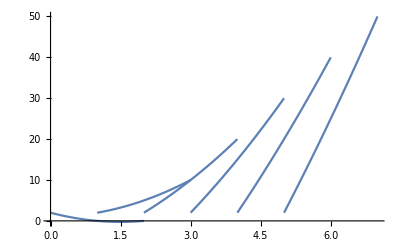

```mathematica
Module[{f,s,A1,B1,C1,F},

f[x_]=a*x^2+b*x+c;

s=Quiet@Solve[f[i]==2&&f[i+1]==5*i&&f[i+2]==10*i,{a,b,c}][[1]];

A1=a/.s;B1=b/.s;C1=c/.s;

F[x_]=A1*x^2+B1*x+C1;

Show[Table[Plot[F[x],{x,i,i+2}],{i,0,5}],PlotRange->All]
(*Table[Evaluate[a/.s],{i,0,5}]*)
]
```

```mathematica
Module[{f,s,A1,B1,C1,F},
(*{a,b,c}={{1,1,1},{2,2,2},{3,3,3}};*)

f[x_]=(a*x^2+b*x+c)/.{a,b,c}->{{1,1,1},{2,2,2},{3,3,3}};

Plot[f[x],{x,0,10}]
]
```

-Graphics-

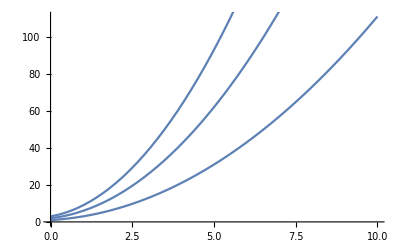

```mathematica
Show[Table[Plot[i*x^2+i*x+i,{x,0,10}],{i,1,3}]]
```